```mathematica
SetDirectory["/home/anthony/Proyectos/Tropical/Code/tropical-geometry/Outputs"];
Import["/home/anthony/Proyectos/Tropical/Code/tropical-geometry/MathematicaCode/functions_TropGraph.wl"]
```

```mathematica
hf3=hyperPlanes["f3"];
bf3=bVec["f3"];
ptHull=extremalVert["f3"];
lfNf3=lowerFaces["f3"];
```

```mathematica
plotSubdiv[lfNf3,ptHull]
```

-Graphics3D-

```mathematica
plotSubdivHyp[lfNf3, hf3, bf3, {1,1,1},1.5]
```

-Graphics3D-

```mathematica
hf2= hyperPlanes["f2"];
bf2=bVec["f2"];
ptHull2 = extremalVert["f2"];
lfNf2 = lowerFaces["f2"];
```

```mathematica
plotSubdiv[lfNf2,ptHull2]
```

-Graphics3D-

```mathematica
plotSubdivHyp[lfNf2,hf2,bf2,{1,1,0},3]
```

-Graphics3D-

```mathematica
hf1= hyperPlanes["f1"];
bf1=bVec["f1"];
ptHull1 = extremalVert["f1"];
lfNf1 = lowerFaces["f1"];
```

```mathematica
plotSubdiv[lfNf1,ptHull1]
```

-Graphics3D-

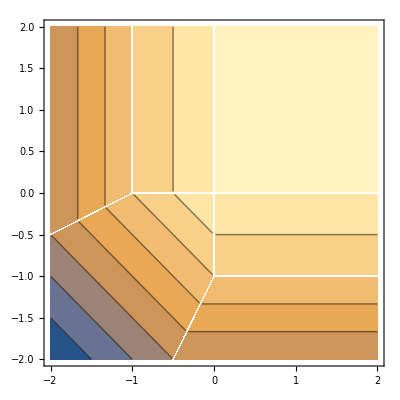

```mathematica
u=0;
ContourPlot[Min[2x+1+2u,2y+1+2u,2x+2y+1,3y+2+u,3x+2+u,x+y+3+2u,2y+x+3+u,1+4u],{x,-2,2},{y,-2,2}]
```